```mathematica
SetDirectory[NotebookDirectory[]];
```

Lattice

### Visualize a lattice

```mathematica
visualizeLattice[lattice_,boxLength_,speciesLimit_:None]:=Module[
{m,colDict,cols,colVal},
colDict=Association[];
cols=If[speciesLimit===None,
Sort[DeleteDuplicates[Values[lattice]]],
Sort[DeleteDuplicates[speciesLimit]]
];
colVal=0.0;
Do[
colDict[col]=colVal;
If[col≠cols[[-1]],
colVal+=1.0/(Length[cols]-1);
];
,{col,cols}];

m=ConstantArray[0,{boxLength,boxLength,boxLength}];
Do[
If[speciesLimit===None,
m[[l[[1]],l[[2]],l[[3]]]]=lattice[l];
,
If[MemberQ[speciesLimit,lattice[l]],
m[[l[[1]],l[[2]],l[[3]]]]=lattice[l];
];
];
,{l,Keys[lattice]}];

(* Multicolor *)
Return[Graphics3D[First@Last@Reap[MapIndexed[If[#≠0,Sow[{ColorData["BrightBands"][colDict[#]],Cuboid[#2]}]]&,m,-1]],PlotRange->{{1,boxLength+1},{1,boxLength+1},{1,boxLength+1}},ImageSize->Small]];

(* Unicolor *)
(*
Return[Graphics3D[First@Last@Reap[MapIndexed[If[#≠0,Sow[Cuboid[#2]]]&,m,-1]],PlotRange->{{1,boxLength+1},{1,boxLength+1},{1,boxLength+1}},ImageSize->Small]];
*)
];
```

### Lattice

#### Box len

```mathematica
boxLength=26;
```

#### Initial

```mathematica
latt=Import["latt_0000.txt","Table"];
lattDict=Association[];
Do[
lattDict[l[[;;3]]]=l[[4]];
,{l,latt}];
```

```mathematica
visualizeLattice[lattDict,boxLength,{"X","Y","Z"}]
```

-Graphics3D-

#### Second

```mathematica
latt=Import["latt_0100.txt","Table"];
lattDict=Association[];
Do[
lattDict[l[[;;3]]]=l[[4]];
,{l,latt}];
```

```mathematica
visualizeLattice[lattDict,boxLength,{"X","Y","Z"}]
```

-Graphics3D-

Particle counts

```mathematica
x=Flatten[Import["X.txt","Table"]];
y=Flatten[Import["Y.txt","Table"]];
z=Flatten[Import["Z.txt","Table"]];
```

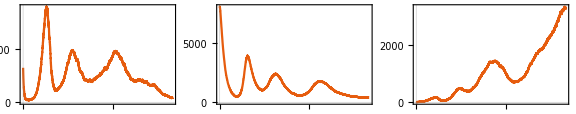

```mathematica
GraphicsRow[{
ListLinePlot[x,PlotRange->All],
ListLinePlot[y,PlotRange->All],
ListLinePlot[z,PlotRange->All]
},ImageSize->Large]
```

```mathematica
dat=Transpose[{x,y,z}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat]
```

-Graphics3D-

Reaction counts

```mathematica
rxn=Association[];
rxn["rm3"]=Flatten[Import["rxnM3.txt","Table"]];
rxn["rm4"]=Flatten[Import["rxnM4.txt","Table"]];
rxn["rp1"]=Flatten[Import["rxnP1.txt","Table"]];
rxn["rm1"]=Flatten[Import["rxnM1.txt","Table"]];
rxn["rp2"]=Flatten[Import["rxnP2.txt","Table"]];
rxn["rm2"]=Flatten[Import["rxnM2.txt","Table"]];
rxn["rp3"]=Flatten[Import["rxnP3.txt","Table"]];
rxn["rp4"]=Flatten[Import["rxnP4.txt","Table"]];
rxn["rp5"]=Flatten[Import["rxnP5.txt","Table"]];
rxn["rm5"]=Flatten[Import["rxnM5.txt","Table"]];
```

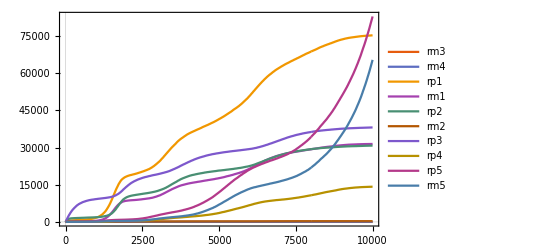

```mathematica
ListLinePlot[rxn,PlotLegends->Keys[rxn]]
```